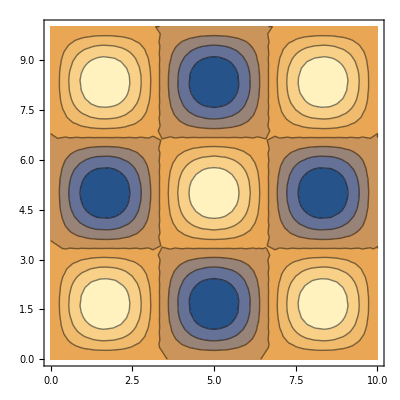

```mathematica
ψ[x_,nx_]:=√(2/L)*Sin[(nx*π)/L x];
ψ[y_,ny_]:=√(2/L)*Sin[(ny*π)/L y];

ψ[z_,nz_]:=√(2/L)*Sin[(nz*π)/L z];


L=10;
ContourPlot[ψ[x,3]ψ[y,3],{x,0,10},{y,0,10}]
```

```mathematica
Plot3D[ψ[x,3]ψ[y,1],{x,0,10},{y,0,10}]
```

-Graphics3D-

```mathematica
Manipulate[ContourPlot[ψ[x,nx]ψ[y,ny],{x,0,10},{y,0,10}],{nx, 1,10,1},{ny,1,10,1},ControlType->PopupMenu]
```

```mathematica
Manipulate[Plot3D[ψ[x,nx]ψ[y,ny],{x,0,10},{y,0,10}],{nx, 1,10,1},{ny,1,10,1},ControlType->PopupMenu]
```